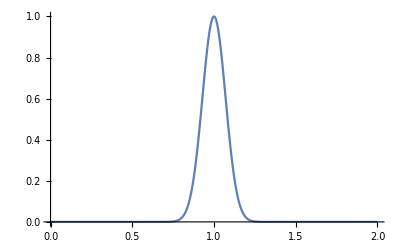

0.0886227 Erf[10. (-1.+x)]

```mathematica
(* FUNCAO 1 *)
f[x_]=E^(-((x-1)^2/ξ));
ξ=0.01;
Plot[f[x],{x,0,2},PlotRange->All]

solnum=Integrate[f[x],x]
```

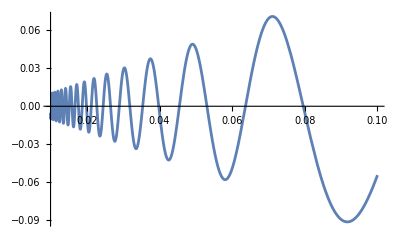

```mathematica
(* FUNCAO 2 *)
Clear[x]
g[x_]=x Sin[1/x];
Plot[g[x],{x,1/100,0.1}, PlotRange->All]
funcint=Integrate[g[x],{x,1/10,0,1}];
```

```mathematica
F[x_]=1.25 Sin[x/2]+1;
Plot [F[x],{x,0,12},PlotRange->All];
```

## Simpsons Rule

```mathematica
d[x_]=E^(-x^2);
solexact=NIntegrate[d[x],{x,-1,1}];
(*Número de puntos*)
n=4;
(*Límites de integración*)
a=-1;
b=1;

h=(b-a)/n;

tabela=Table[d[x],{x,a,b,h}];
indices=Table[i,{i,2,n,1}]
solaprox=h/3(tabela[[1]]+tabela[[-1]]);
tabela[[indices[[1]]]]
```

{2,3,4}

1/ⅇ^(1/4)

```mathematica
ClearAll[Simpson13]

Simpson13[f_,a_,b_,n_]:=Module[{h,x,sum},h=(b-a)/n;
x=Table[a+i*h,{i,0,n}];
sum=f[a]+f[b];
sum+=4 Total[f/@x[[2;;-2;;2]]];
sum+=2 Total[f/@x[[1;;-1;;2]]];
sum*h/3]
f[x_]:=E^(-x^2); (*Define la función que deseas integrar aquí*)

a=-1; (*Límite inferior del intervalo de integración*)
b=1; (*Límite superior del intervalo de integración*)
n=4; (*Número de subdivisiones del intervalo*)

resultado=Simpson13[f,a,b,n]//N
```

1.73961

```mathematica
num={0,1,2,3};
```

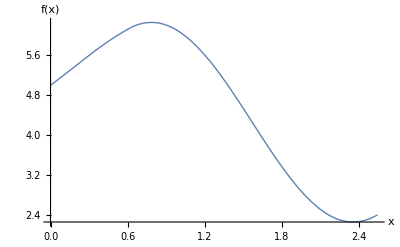

```mathematica
(* FUNCAO 3 *)
Clear[x,f]

w[x_]=Piecewise[{{2x+5,0<= x<1/Pi},{((-5 Pi^2(x^2-2x-5))+10 Pi x+2x )/(1+5 Pi^2),1/Pi<=x<2/Pi},{(2 Sin[2 x]+((4+20 Pi^2+25 Pi^3)/(Pi+5 Pi^3)))-2 Sin[4/Pi],2/Pi<=x<=8/Pi}
}];
plot2=Plot[w[x],{x,0,8/Pi},PlotStyle->Thick,AxesLabel->{"x","f(x)"}]
```

```mathematica
g[x_]=Integrate[w[x],x]//FullSimplify

1.0/Pi
2.0/Pi
8.0/Pi
```

Piecewise[{{x (5+x), 0<x≤1/π}, {(5+π x (3 x+5 π (3 x+π (15-(-3+x) x))))/(3 (π+5 π^3)), 1/π<x≤2/π}, {(84+5 π (5+12 π (7+10 π)))/(3 (π^2+5 π^4))+Cos[4/π]-Cos[16/π]-(12 Sin[4/π])/π, π x>8}, {(-12+π (25+12 x+3 π (-20+5 π (4+5 π) x+(1+5 π^2) Cos[4/π]))-3 π (1+5 π^2) (π Cos[2 x]+2 (-2+π x) Sin[4/π]))/(3 (π^2+5 π^4)), π x>2&&π x≤8}, {0, True}}]

0.31831

-0.653644

```mathematica
Plot[g[x],{x,0,8/Pi}];
g[0.47746482927568601];
g[0.63661977236758138];
Table[{x,g[x]},{x,0,8/Pi, (8/(20.Pi))}]
```

{{0.,0},{0.127324,0.652831},{0.254648,1.33809},{0.381972,2.05568},{0.509296,2.80359},{0.63662,3.57785},{0.763944,4.37077},{0.891268,5.16646},{1.01859,5.94859},{1.14592,6.70172},{1.27324,7.41228},{1.40056,8.06942},{1.52789,8.66577},{1.65521,9.19787},{1.78254,9.66638},{1.90986,10.0761},{2.03718,10.4356},{2.16451,10.7567},{2.29183,11.0536},{2.41916,11.3423},{2.54648,11.6391}}

```mathematica
TrapeciosIntegrate[a_,b_,ref_]:=Block[{fa=a, fb=b, fref=ref,puntos,AreasT,AreasR,fnel,Error },
fnel= 2^fref;
h = (fb-fa)/fnel;
puntos = Table[{fa+( q*h),w[fa+( q*h)]},{q,0,fnel,1}];
AreasT = Table[{i,(1/2)(puntos[[i+1,2]]+puntos[[i,2]])*(puntos[[i+1,1]]-puntos[[i,1]]) },{i,1,fnel,1}];
AreasR = Table[{i,NIntegrate[w[x],{x,puntos[[i,1]],puntos[[i+1,1]] }] },{i,1,fnel,1}];
Error = Table[{i, Abs[AreasT[[i,2]]-AreasR[[i,2]] ]},{i,1,fnel,1}];
Return[{puntos, AreasT, AreasR,Error}]
];
```

{{{0.,5.},{0.3125,5.625},{0.625,6.15781},{0.9375,6.16999},{1.25,5.45876},{1.5625,4.295},{1.875,3.1187},{2.1875,2.37458},{2.5,2.34397}},{{1,1.66016},{2,1.84106},{3,1.92622},{4,1.81699},{5,1.52403},{6,1.15839},{7,0.858324},{8,0.737273}},{{1,1.66016},{2,1.84604},{3,1.94666},{4,1.83343},{5,1.53054},{6,1.15252},{7,0.842284},{8,0.717132}},{{1,1.9984×10^-15},{2,0.00498014},{3,0.0204434},{4,0.0164358},{5,0.00651122},{6,0.00587504},{7,0.0160401},{8,0.0201408}}}

{{1,1.3125},{2,1.43346},{3,1.52806},{4,1.54215},{5,1.4424},{6,1.25035},{7,1.01304},{8,0.788558},{9,0.631872},{10,0.581341}}

{{1,1.3125},{2,1.43554},{3,1.53546},{4,1.55234},{5,1.45045},{6,1.2543},{7,1.01192},{8,0.782642},{9,0.622607},{10,0.570997}}

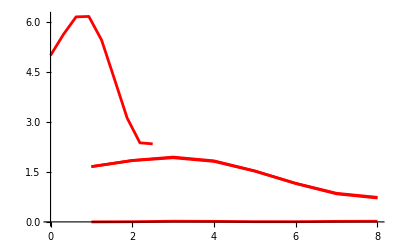

```mathematica
tpoint=TrapeciosIntegrate[0,2.5,3]
AreasT
AreasR
plot1=ListPlot[tpoint, Joined->True, PlotStyle->Red]
```

```mathematica
Manipulate[Show[plot2, ListPlot[TrapeciosIntegrate[0,2.5,jose][[1]], Joined->True, PlotStyle->Red,Filling->Axis]],{jose,2,10,1}]
```

ListPlot::lpn: 0. is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[plot2,ListPlot[0,Joined→True,PlotStyle→color,Filling→Axis]].

ListPlot::lpn: 0. is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[plot2,ListPlot[0,Joined→True,PlotStyle→color,Filling→Axis]].

ListPlot::lpn: 0. is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[,ListPlot[0,Joined→True,PlotStyle→color,Filling→Axis]].

```mathematica
(*Simpson 1/3*)
Sim[a_,b_,ref]:=Block[{fa=a,fb=b,fref=ref}
fnel= 2^fref;
h = (fb-fa)/fnel;
puntos = Table[{fa+( q*h),w[fa+( q*h)]},{q,0,fnel,1}];
AreasT = Table[{i,(1/2)(puntos[[i+1,2]]+puntos[[i,2]])*(puntos[[i+1,1]]-puntos[[i,1]]) },{i,1,fnel,1}];
AreasR = Table[{i,NIntegrate[w[x],{x,puntos[[i,1]],puntos[[i+1,1]] }] },{i,1,fnel,1}];
Error = Table[{i, Abs[AreasT[[i,2]]-AreasR[[i,2]] ]},{i,1,fnel,1}];
Return[{puntos, AreasT, AreasR,Error}]
];
```

```mathematica
gab={1,2,3}//MatrixForm
gab[[1,3]]
```

(1
2
3)

3

```mathematica
g[x]
```

Piecewise(List(List(x*(5 + x),
     Inequality(0,Less,x,LessEqual,1/Pi)),
    List((5 + Pi*x*(3*x + 5*Pi*(3*x + Pi*(15 - (-3 + x)*x))))/
      (3.*(Pi + 5*Power(Pi,3))),
     Inequality(1/Pi,Less,x,LessEqual,2/Pi)),
    List((84 + 5*Pi*(5 + 12*Pi*(7 + 10*Pi)))/
       (3.*(Power(Pi,2) + 5*Power(Pi,4))) + Cos(4/Pi) - 
      Cos(16/Pi) - (12*Sin(4/Pi))/Pi,Pi*x > 8),
    List((-12 + Pi*(25 + 12*x + 
           3*Pi*(-20 + 5*Pi*(4 + 5*Pi)*x + 
              (1 + 5*Power(Pi,2))*Cos(4/Pi))) - 
        3*Pi*(1 + 5*Power(Pi,2))*
         (Pi*Cos(2*x) + 2*(-2 + Pi*x)*Sin(4/Pi)))/
      (3.*(Power(Pi,2) + 5*Power(Pi,4))),Pi*x > 2 && Pi*x <= 8)),
   0)